```mathematica
P[v_, I_]:=v^3+2 v^2-I-1
```

```mathematica
P[0, 0]
```

-1

```mathematica
Δ[a_]:=-(a+1)(a-5/27)
```

```mathematica
v1[a_]:=2/3(2*Cos[1/3 ArcCos[(11+27*a)/16]]-1)
v2[a_]:=2/3(2*Cos[1/3 ArcCos[(11+27*a)/16]+2 π/3]-1)
v3[a_]:=2/3(2*Cos[1/3 ArcCos[(11+27*a)/16]+4 π/3]-1)
```

```mathematica
w1[a_]:= 9/4(1/9+a)
w2[a_]:= -9/8(1+a)
```

```mathematica
j = ⅇ^((2*I*π)/3);
x1[a_]:=2 Abs[-11/27-a]/(11/27+a)2/3 Cosh[1/3 ArcCosh[27/16 Abs[-11/27-a]]]-2/3;
```

```mathematica
x1[-2] // N
```

-2.20557

```mathematica
v1[-2]//N
v2[-2]//N
v3[-2]//N
```

0.102785+0.665457 ⅈ

-2.20557+4.70511×10^-17 ⅈ

0.102785-0.665457 ⅈ

Pour Δ = 0

```mathematica
w1[-1]//N
w2[-1]//N
```

-2.

0.

```mathematica
w1[5/27]//N
w2[5/27]//N
```

0.666667

-1.33333

Pour I = -1 (Δ = 0)

```mathematica
x1[-1.1] // N
```

-2.0244

```mathematica
x1[-1] // N
```

-2.

```mathematica
v1[-1]//N
v2[-1]//N
v3[-1]//N
```

0.

-2.

0.

```mathematica
v1[-0.9]//N
v2[-0.9]//N
v3[-0.9]//N
```

0.212593

-1.97435

-0.238247

Pour I = 5/27 (Δ = 0)

```mathematica
x1[5/27] // N
```

0.666667

```mathematica
x1[5/27+0.01] // N
```

0.66916

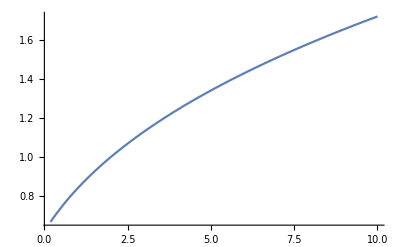

```mathematica
P1 = Plot[x1[x], {x, 5/27, 10}]
```

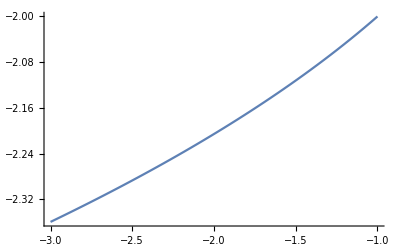

```mathematica
P2 = Plot[x1[x], {x, -3, -1}]
```

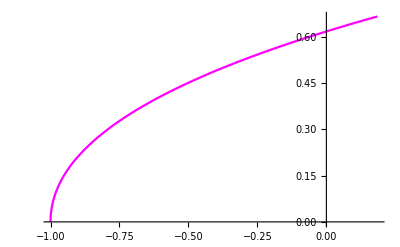

```mathematica
P11 = Plot[v1[x], {x, -1, 5/27}, PlotStyle->Magenta]
```

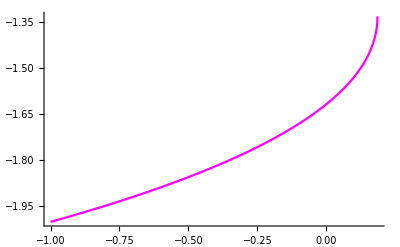

```mathematica
P12 = Plot[v2[x], {x, -1, 5/27}, PlotStyle->Magenta]
```

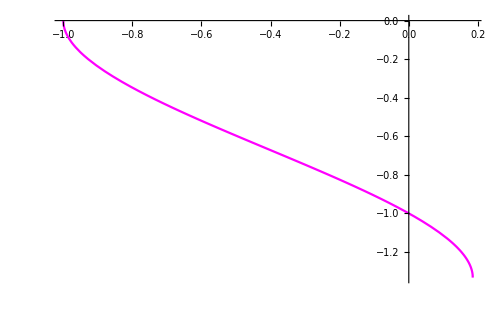

```mathematica
P13 = Plot[v3[x], {x, -1, 5/27}, PlotStyle->Magenta]
```

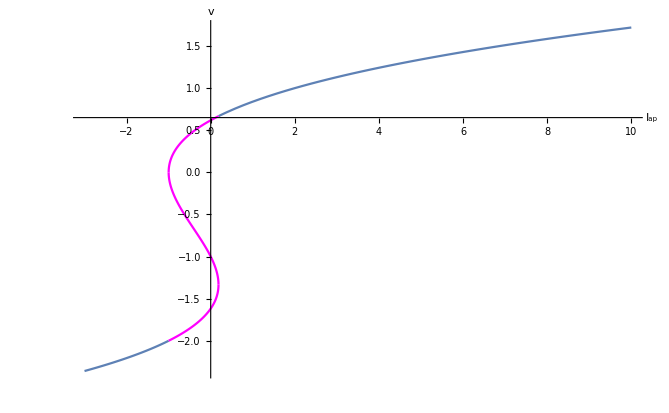

graphics.pdf

```mathematica
Show[P1, P2, P11, P12, P13, PlotRange->All, AxesLabel->{"I_ap",v}, GridLines->{{-1,5/27}, {}}]
Export["graphics.pdf",%]
```

Par la methode de Cardan (https://brilliant.org/wiki/cardano-method/)

```mathematica
a = 1;
b = 0;
c = -4/3;
d = -(11/27+Subscript[i, ap]);
```

```mathematica
Q = (3*a*c-b^2)/(9*a^2);
```

```mathematica
R = (9*a*b*c-27*a^2*d-2*b^3)/(54*a^3);
```

```mathematica
S = (R+√(Q^3+R^2))^(1/3);
R = (R-√(Q^3+R^2))^(1/3);
```

```mathematica
s1 = S + T - b/(3a);
s2 = -(S+T)/2
```